{{F→Function[{x,t},(-x-r t λ+r t x λ)/(-1-r t λ+r t x λ)]}}

Piecewise[{{((r t λ)/(1+r t λ))^(-1+m)/(1+r t λ)^2, m≥1}, {-((r t λ)/(1+r t λ))^m/(1+r t λ), 0<m<1}, {(r t λ)/(1+r t λ), m==0}, {0, True}}]

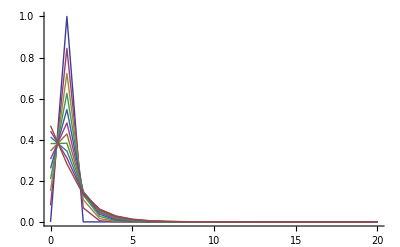

```mathematica
DSolve[{D[F[x,t], t]==λ r (1-x)^2 D[F[x,t], x],F[x,0]==x},F,{x,t}]
FullSimplify[SeriesCoefficient[F[x,t]/.%⟦1⟧,{x,0,m}]]
ListPlot[Table[Table[{m,SeriesCoefficient[F[x,t]/.%%⟦1⟧,{x,0,m}]},{m,0,20}] /. {λ->1.1,r->0.08},{t,0,10}],Joined->True,PlotRange->All]
```

{{F→Function[{z,t},ⅇ^(-t (λ-z λ))]}}

Piecewise[{{DifferenceRoot[Function[{y,n},{-t λ y[n]+(1+n) y[1+n]==0,y[0]==ⅇ^(-t λ)}]][g], g≥0}, {0, True}}]

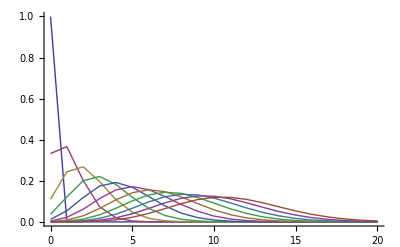

```mathematica
DSolve[{D[F[z,t], t]==(z-1) λ F[z,t],F[z,0]==1},F,{z,t}]
FullSimplify[SeriesCoefficient[F[z,t]/.%⟦1⟧,{z,0,g}]]
ListPlot[Table[Table[{m,SeriesCoefficient[F[z,t]/.%%⟦1⟧,{z,0,m}]},{m,0,20}]/.{λ->1.1} ,{t,0,10}] ,Joined->True,PlotRange->All]
```

```mathematica
DSolve[{D[ξ[τ],τ] == λ (r z (ξ[τ]^2-1) + ξ[τ](1-z)),ξ[t]==x}, ξ,τ]
ξ[0] /. %[[1]] //FullSimplify
Table[SeriesCoefficient[%,{x,0,m},{z,0,g}],{m,0,5},{g,0,5}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ξ→Function[{τ},1/(2 r z)(-1+z+√(-1+2 z-z^2-4 r^2 z^2) Tan[1/2 (√(-1+2 z-z^2-4 r^2 z^2) λ τ+1/(1-2 z+z^2+4 r^2 z^2)√(-1+2 z-z^2-4 r^2 z^2) (-t λ+2 t z λ-t z^2 λ-4 r^2 t z^2 λ-2 √(-1+2 z-z^2-4 r^2 z^2) ArcTan[(-√(-1+2 z-z^2-4 r^2 z^2)+z √(-1+2 z-z^2-4 r^2 z^2)-2 r x z √(-1+2 z-z^2-4 r^2 z^2))/(1-2 z+z^2+4 r^2 z^2)]))])]}}

(-1+z-√(-1-z (-2+z+4 r^2 z)) Tan[1/2 t √(-1-z (-2+z+4 r^2 z)) λ-ArcTan[(1-z+2 r x z)/(√(-1-z (-2+z+4 r^2 z)))]])/(2 r z)